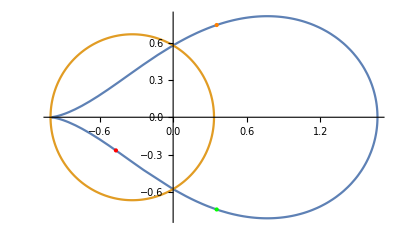

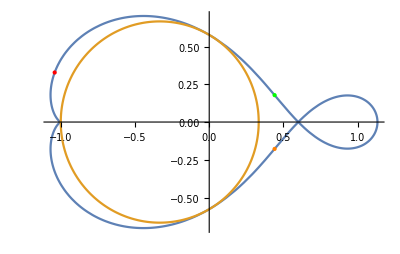

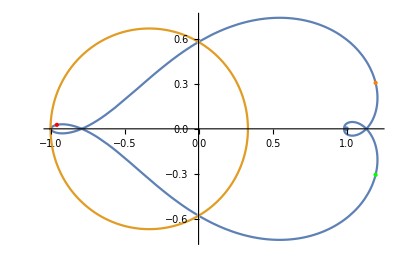

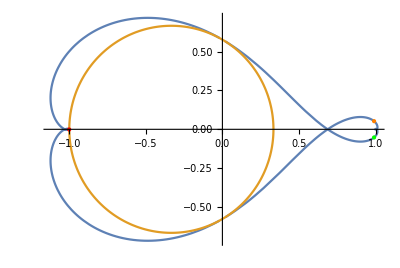

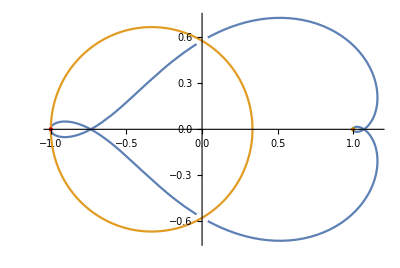

```mathematica
z[x_]:=2/3(Cos[x]+I*Sin[x])-1/3
g[x_]:=z[x]
F[x_]:=(x+1/x)(1/2)

For[i=0;t[x_]:=Nest[F,g[x],i];
h[x_]:=Nest[F,g[x],i-1],i<5,i++;
punto1=Graphics[{PointSize[Large],Red,Point[ReIm[t[Pi/2]]]}];
punto2=Graphics[{PointSize[Large],Green,Point[ReIm[t[Pi/4]]]}];
punto3=Graphics[{PointSize[Large],Orange,Point[ReIm[t[-Pi/4]]]}];
grafico=ParametricPlot[{ReIm[t[x]],ReIm[z[x]]},{x,0,2Pi}];
Print[Show[{grafico,punto1,punto2,punto3}]]]
```

```mathematica
z[Pi/2]
```

```mathematica
z[π/2]
```

-1/3+(2 ⅈ)/3

```mathematica
F[-1/3+(2 ⅈ)/3]
```

-7/15-(4 ⅈ)/15